```mathematica
a={{2010,3070000},{2011,3070000},{2012,2840000},{2013,2764000},{2014,2732000},{2015,2732000},{2016,2726000},{2017,2498000},{2018,2358000},{2019,2236000},{2020,1993000},{2021,1814000},
{2022,1649000},{2023,1409000},{2024,1338000}};
```

```mathematica
(* year 2011 has no circulation data, previous year circulation employed for 2011 *)
```

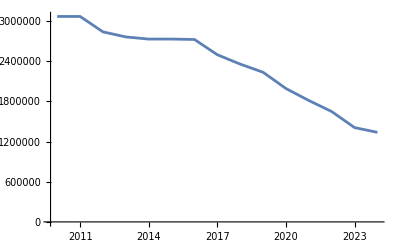

```mathematica
ListPlot[a,Joined->True]
```

```mathematica
b={{2010,100000},{2011,170000},{2012,250000},{2013,335000},{2014,390000},{2015,449000},{2016,501000},{2017,558000},{2018,620000},{2019,698000},{2020,760000},{2021,797000},{2022,823000},{2023,902000},{2024,1020000}}
```

{{2010,100000},{2011,170000},{2012,250000},{2013,335000},{2014,390000},{2015,449000},{2016,501000},{2017,558000},{2018,620000},{2019,698000},{2020,760000},{2021,797000},{2022,823000},{2023,902000},{2024,1020000}}

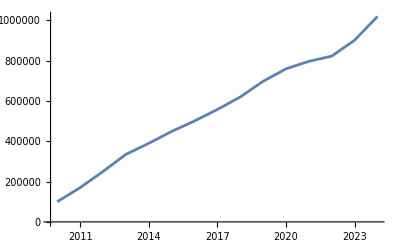

```mathematica
ListPlot[b,Joined->True]
```

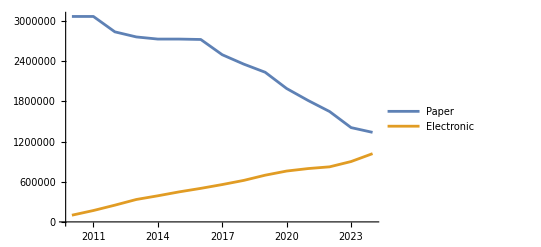

```mathematica
ListPlot[{a,b},Joined->True,PlotLegends->LineLegend[{"Paper","Electronic"}]]
```

```mathematica
pc=5500
```

5500

```mathematica
ec=4277
```

4277

```mathematica
a2=Transpose[a]
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{3070000,3070000,2840000,2764000,2732000,2732000,2726000,2498000,2358000,2236000,1993000,1814000,1649000,1409000,1338000}}

```mathematica
a3={a2[[1]],12*pc*a2[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{202620000000,202620000000,187440000000,182424000000,180312000000,180312000000,179916000000,164868000000,155628000000,147576000000,131538000000,119724000000,108834000000,92994000000,88308000000}}

```mathematica
a4=Transpose[a3]
```

{{2010,202620000000},{2011,202620000000},{2012,187440000000},{2013,182424000000},{2014,180312000000},{2015,180312000000},{2016,179916000000},{2017,164868000000},{2018,155628000000},{2019,147576000000},{2020,131538000000},{2021,119724000000},{2022,108834000000},{2023,92994000000},{2024,88308000000}}

```mathematica
b2=Transpose[b]
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{100000,170000,250000,335000,390000,449000,501000,558000,620000,698000,760000,797000,823000,902000,1020000}}

```mathematica
b3={b2[[1]],12*ec*b2[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{5132400000,8725080000,12831000000,17193540000,20016360000,23044476000,25713324000,28638792000,31820880000,35824152000,39006240000,40905228000,42239652000,46294248000,52350480000}}

```mathematica
b4=Transpose[b3]
```

{{2010,5132400000},{2011,8725080000},{2012,12831000000},{2013,17193540000},{2014,20016360000},{2015,23044476000},{2016,25713324000},{2017,28638792000},{2018,31820880000},{2019,35824152000},{2020,39006240000},{2021,40905228000},{2022,42239652000},{2023,46294248000},{2024,52350480000}}

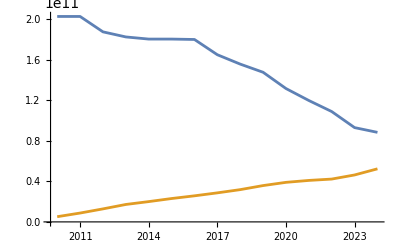

```mathematica
ListPlot[{a4,b4},Joined->True]
```

```mathematica
c={a2[[1]],a3[[2]]+b3[[2]]}
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{207752400000,211345080000,200271000000,199617540000,200328360000,203356476000,205629324000,193506792000,187448880000,183400152000,170544240000,160629228000,151073652000,139288248000,140658480000}}

```mathematica
c4=Transpose[c]
```

{{2010,207752400000},{2011,211345080000},{2012,200271000000},{2013,199617540000},{2014,200328360000},{2015,203356476000},{2016,205629324000},{2017,193506792000},{2018,187448880000},{2019,183400152000},{2020,170544240000},{2021,160629228000},{2022,151073652000},{2023,139288248000},{2024,140658480000}}

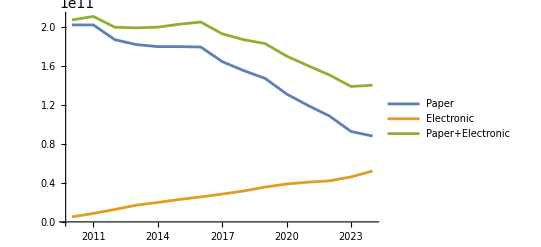

```mathematica
ListPlot[{a4,b4,c4},Joined->True,PlotLegends->LineLegend[{"Paper","Electronic","Paper+Electronic"}]]
```

```mathematica
MatrixForm[a]
```

(2010 | 3070000
2011 | 3070000
2012 | 2840000
2013 | 2764000
2014 | 2732000
2015 | 2732000
2016 | 2726000
2017 | 2498000
2018 | 2358000
2019 | 2236000
2020 | 1993000
2021 | 1814000
2022 | 1649000
2023 | 1409000
2024 | 1338000)

```mathematica
MatrixForm[b]
```

(2010 | 100000
2011 | 170000
2012 | 250000
2013 | 335000
2014 | 390000
2015 | 449000
2016 | 501000
2017 | 558000
2018 | 620000
2019 | 698000
2020 | 760000
2021 | 797000
2022 | 823000
2023 | 902000
2024 | 1020000)

```mathematica
?Export
```

```mathematica
Export["~/nikkei-pc.csv",a,"CSV"]
```

~/nikkei-pc.csv

```mathematica
Export["~/nikkei-ec.csv",b,"CSV"]
```

~/nikkei-ec.csv

```mathematica
Export["~/nikkei-ps.csv",a4,"CSV"]
```

~/nikkei-ps.csv

```mathematica
Export["~/nikkei-es.csv",b4,"CSV"]
```

~/nikkei-es.csv

```mathematica
Export["~/nikkei-pes.csv",c4,"CSV"]
```

~/nikkei-pes.csv

```mathematica
?LeastSquares
```

```mathematica
a[[1]]
```

{2010,3070000}

```mathematica
as=Table[a[[i]],{i,7,Length[a]}]
```

{{2016,2726000},{2017,2498000},{2018,2358000},{2019,2236000},{2020,1993000},{2021,1814000},{2022,1649000},{2023,1409000},{2024,1338000}}

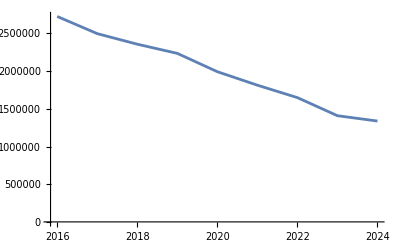

```mathematica
g1=ListPlot[as,Joined->True]
```

```mathematica
f[t_]=Fit[as,{1,t},t]
```

3.60855×10^8-177650. t

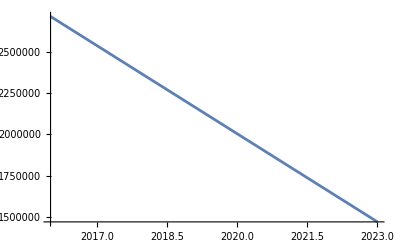

```mathematica
g2=Plot[f[t],{t,2016,2023}]
```

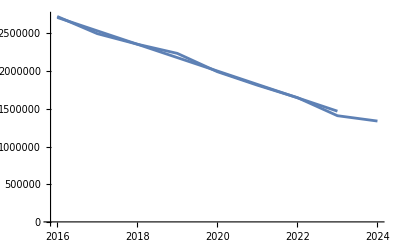

```mathematica
Show[g1,g2,PlotLegends->LineLegend[{"Paper data","approximation with line"}]]
```

```mathematica
Solve[f[t]==1000000,t]
```

{{t→2025.64}}

```mathematica
Solve[f[t]==800000,t]
```

{{t→2026.77}}

```mathematica
Solve[f[t]==500000,t]
```

{{t→2028.46}}

```mathematica
Solve[f[t]==0,t]
```

{{t→2031.27}}

```mathematica
b
```

{{2010,100000},{2011,170000},{2012,250000},{2013,335000},{2014,390000},{2015,449000},{2016,501000},{2017,558000},{2018,620000},{2019,698000},{2020,760000},{2021,797000},{2022,823000},{2023,902000},{2024,1020000}}

```mathematica
g[t_]=Fit[b,{1,t},t]
```

-1.23862×10^8+61685.7 t

```mathematica
-1.2186968791208708*^8+60696.70329670291 t
```

-1.2187×10^8+60696.7 t

```mathematica
g3=ListPlot[b,Joined->True]
```

-Graphics-

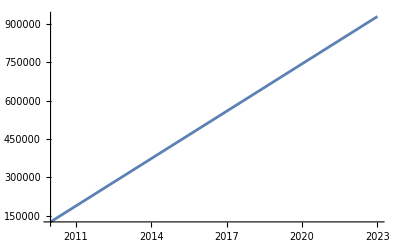

```mathematica
g4=Plot[g[t],{t,2010,2023}]
```

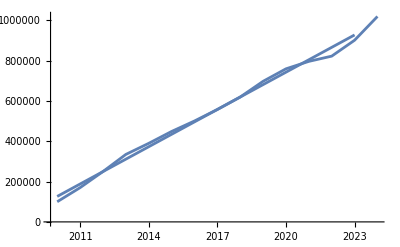

```mathematica
Show[g3,g4]
```

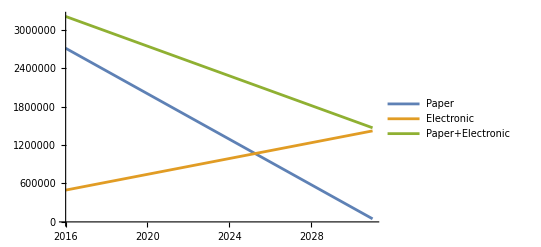

```mathematica
Plot[{f[t],g[t],f[t]+g[t]},{t,2016,2031},PlotLegends->LineLegend[{"Paper","Electronic","Paper+Electronic"}]]
```

```mathematica
Solve[f[t]+g[t]==0,t]
```

{{t→2043.68}}

```mathematica
at=Transpose[a]
```

{{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},{3070000,3070000,2840000,2764000,2732000,2732000,2726000,2498000,2358000,2236000,1993000,1814000,1649000,1409000,1338000}}

```mathematica
da=Table[at[[2,i+1]]-at[[2,i]],{i,2,Length[at[[2]]]-1}]
```

{-230000,-76000,-32000,0,-6000,-228000,-140000,-122000,-243000,-179000,-165000,-240000,-71000}

```mathematica
tt=Table[at[[1,i]],{i,3,Length[at[[1]]]}]
```

{2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024}

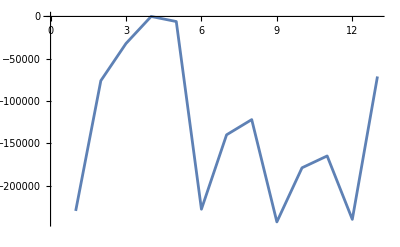

```mathematica
ListPlot[da,Joined->True]
```